# Comp Bio Homework 1

## Problem 1 : Time delayed model with Allee effect

## a) Show examples of the different dynamics obtained in this model :

Allee  effect  model 
-Graphics-

- no oscillations
- damped oscillations
- stable oscillations

NDSolveValue::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

General::stop: Further output of NDSolveValue::ihist will be suppressed during this calculation.

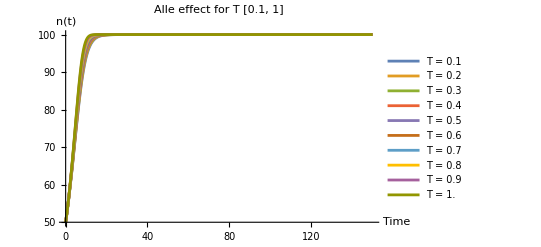

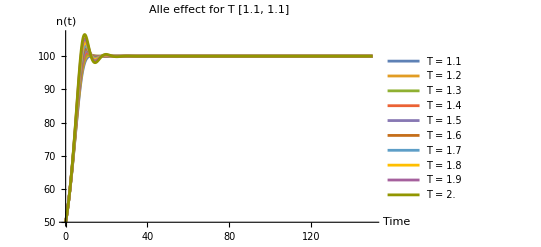

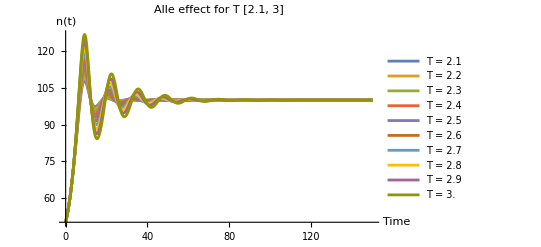

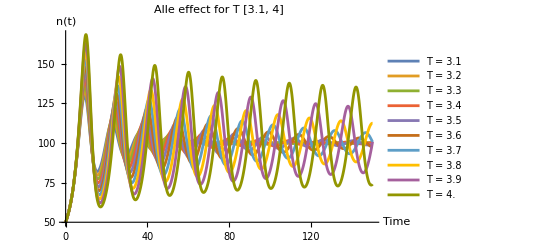

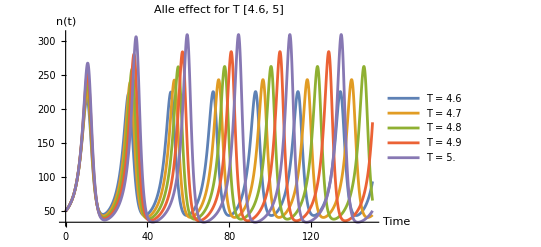

```mathematica
ClearAll["Global`*"];

(*Define parameters*)
A=20;
K=100;
r=0.1;

(* Determine T values*)
TValues = Range[0.1,5,0.1];

t0 = 0;
tMax = 300;

(*Initial condition*)
initCond = n[0] == 50;

(*Solve diff equation*)
solveDifferentialEquation[T_] := NDSolveValue[
	{n'[t] == r*n[t]*(1 - n[t - T]/K)*(n[t]/A - 1), initCond}, 
    n, {t, t0, tMax}
];

(* solutions for differen T*)
solutions = Table[
	solveDifferentialEquation[T], 
	{T, TValues}
];

tMax = tMax / 2;
Plot[Evaluate[Table[solutions[[i]][t], {i, 1,10}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 1,10}], 
     PlotLabel -> "Alle effect for T [0.1, 1]", 
     AxesLabel -> {"Time", "n(t)"}

]

Plot[Evaluate[Table[solutions[[i]][t], {i, 11,20}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 11, 20}], 
     PlotLabel -> "Alle effect for T [1.1, 1.1]", 
     AxesLabel -> {"Time", "n(t)"}
]

Plot[Evaluate[Table[solutions[[i]][t], {i, 21,30}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 21, 30}], 
     PlotLabel -> "Alle effect for T [2.1, 3]", 
     AxesLabel -> {"Time", "n(t)"}
]

Plot[Evaluate[Table[solutions[[i]][t], {i, 31,40}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 31, 40}], 
     PlotLabel -> "Alle effect for T [3.1, 4]", 
     AxesLabel -> {"Time", "n(t)"}
]

Plot[Evaluate[Table[solutions[[i]][t], {i, 46,50}]], {t, t0, tMax},
     PlotRange -> All, 
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 46, 50}], 
     PlotLabel -> "Alle effect for T [4.6, 5]", 
     AxesLabel -> {"Time", "n(t)"}
]
```

The fives plots each contain the trajectories for different T values. One find that in the case of T small [0.1, 1], there is no osciallation at all. At the value T = 1.1 we slowly see an overshoot, which after a couple of periods is damped completely and goes into a steady state a N = 100. 
In the range T = [3.1, 4] one still observes a dampened behaviour, the oscillation is still exisiting at t = 150, but we see it is enclosed by a shrinking behaviour.
At T = 4.6 one can find an purely oscillating behaviour which is not dampened.

## b) Estimate numerically with one decimal precision the value T at which the dynamics starts exhibiting damped oscillations

As described before, at T = 1.1 a first overshoot can be observed. As this trajectory goes into steady state for longer t, here the first damped oscillation can be observed.
On the other hand, one can clearly say that for  the system has no overshoot. So lets investigate the the values  numerically. 
One finds that when evaluating in the time range  with  a slight overshoot can already be found for , the maximal value reached is  which could be also the result of some numerical inaccuracies.
For  a clear overshoot is found!

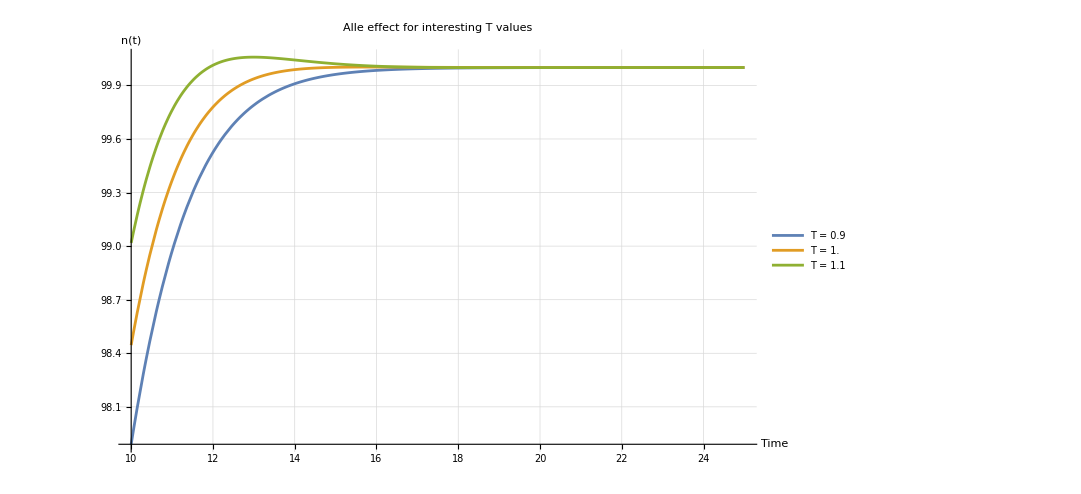

100.

100.003

100.058

```mathematica
Plot[Evaluate[Table[solutions[[i]][t], {i, 9,11}]], {t, 10, 25},
     PlotRange -> All, 
     ImageSize->{800,600},
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 9, 11}],
     PlotLabel -> "Alle effect for interesting T values", 
     GridLines-> Automatic,
     AxesLabel -> {"Time", "n(t)"}
]

(* Find the critical T numerically *)
(* Search for the first trajectory that exceeds the Carrying Capacity K = 100*)
CarryingCapacity = 100;
dT = 0.001;
T9 = Table[solutions[[9]][t], {t, 10, 25, dT}];
T10 = Table[solutions[[10]][t], {t, 10, 25, dT}];
T11 = Table[solutions[[11]][t], {t, 10, 25, dT}];
maxT9 = Max[T9]
maxT10 = Max[T10]
maxT11 = Max[T11]
```

## c) Estimate numerically with one decimal precision the value of T (denoted by TH) at which a bifurcation (Hopf bifurcation) occurs .

A Hopf Bifurcation has happened when periodic solutions arise, namely when a spiral and a limit cycle collide. From the observation in subtask a) we know the interesting behaviour lays in the area around T = 4.5. So lets check a couple of trajectories there

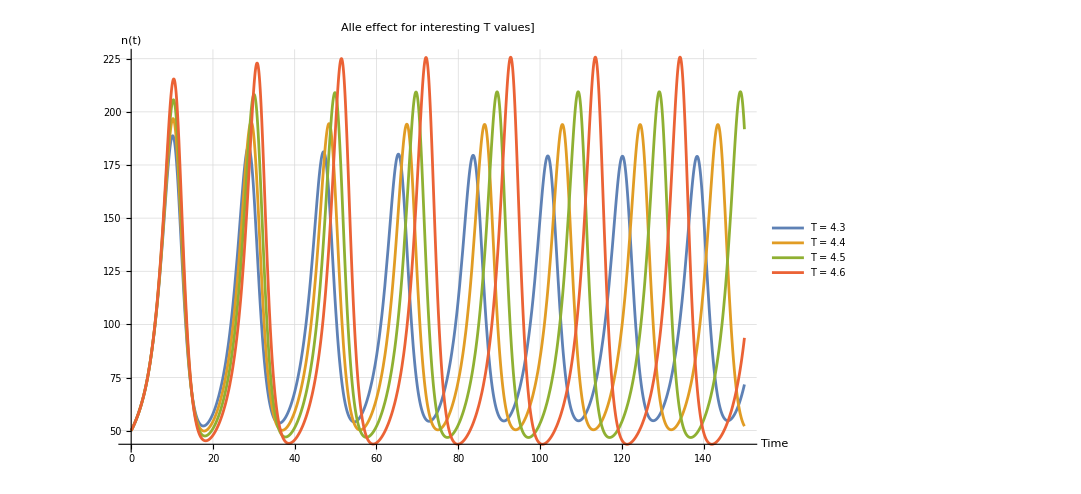

```mathematica
Plot[Evaluate[Table[solutions[[i]][t], {i, 43,46}]], {t, t0, 150},
     PlotRange -> All, 
     ImageSize->{800,600},
     PlotLegends -> Table["T = " <> ToString[TValues[[i]]], {i, 43, 46}],
     PlotLabel -> "Alle effect for interesting T values]", 
     AxesLabel -> {"Time", "n(t)"},
     GridLines->Automatic
]
```

For the trajectory of T = 4.3 one finds a still dampened oscillation. For the trajectory of T = 4.4, we find that there is no increase nor shrinking of the trajectory going on. Very good visible on the grid line of n(t) = 50. For the 2 trajectories T = 4.5 and T = 4.6 we find also perfectly repeating trajectories, they lie on a limit cycle. So the Hopf Bifurcation happens between T = 4.4 - 4.5.

```mathematica
(* Numerically find the bifurcation *)
(* For which value of T does the system get into an undampened state, so that the "peaks" of the periodic trajectories have same amplitude *)
CarryingCapacity = 100;
dT = 0.001;
t0 = 60;
tEnd = 280;
T43 = Table[solutions[[43]][t], {t, t0, tEnd, dT}];
T44 = Table[solutions[[44]][t], {t, t0, tEnd, dT}];
T45 = Table[solutions[[45]][t], {t, t0, tEnd, dT}];
T46 = Table[solutions[[46]][t], {t, t0, tEnd, dT}];
T50 = Table[solutions[[50]][t], {t, t0, tEnd, dT}];
P43 = FindPeaks[T43][[All,2]]
P44 = FindPeaks[T44][[All,2]]
P45 = FindPeaks[T45][[All,2]]
P46 = FindPeaks[T46][[All,2]]
P50 = FindPeaks[T50][[All,2]]
```

{180.101,179.552,179.273,179.13,179.056,179.019,178.999,178.989,178.984,178.981,178.98,178.979,98.1454}

{194.205,194.097,194.053,194.034,194.027,194.024,194.023,194.022,194.022,194.022,194.022,194.022}

{209.342,209.43,209.458,209.467,209.469,209.47,209.47,209.471,209.471,209.471,209.471,61.4968}

{225.592,225.715,225.744,225.75,225.752,225.752,225.753,225.753,225.752,225.752,225.752}

{292.456,309.544,309.548,309.549,309.549,309.549,309.549,309.549,309.549,95.1151}

What was already assumed with the graphical interpretation can be confirmed with the numerical investigation. The trajectories are evaluated for 280 time steps, with a step size . The model with  shows a damped behaviour, whereas from  we find perfectely periodic behaviour without any dampening. Therefore the bifurcation happens at .

## d) Use linear stability analysis to analytically compute the value of T_H. Do this by linearising Eq.(1) around the steady state N* = K and use a pertubation that is proportional to exp(λt). Compare T_H that you obtain analytically to the estimate found in c). Discuss the result.

To find the point of T_H we need to investigate the real part of the eigenvalues of the system. As soon as the sign of the real part of the eigenvalues are changing the Hopf Bifurcation happens.

```mathematica
ClearAll["Global`*"];

(*Define parameters*)
A=20;
K=100;
r=0.1;

(*Determine T values*)
TValues=Range[0.1,5,0.1];

t0=0;
tMax=150;

(*Initial condition*)
initCond=n[0]==50;

(*Define equilibrium point*)
n_eq=K;

(*Define a small perturbation ε*)
e=0.01;

(* define the function *)
nPrime[t_] := r*n[t]*(1-n[t-T]/K)*(n[t]/A-1);

nDoublePrime[†_] = D[nPrime[t], t]

nLin[t_] := nDoublePrime[t]

(*
fLin[n_] := fPrime[K] * (n - K);


Plot[fLin[n[t]], {n[t], 0, 200}]
*)

(*Linearized differential equation*)
(*
linearizedDE=Series[ r*n[t]*(1-n[t-T]/K)*(n[t]/A-1) ,{n,n_eq,0}];
linearizedDE = Normal[linearizedDE]*)
(*
(*Solve linearized equation*)
linearizedSolution=NDSolveValue[{n'[t]==linearizedDE,n[0]==n_eq+e},n,{t,t0,tMax}];

(*Plot the linearized solution*)
Plot[linearizedSolution[t],{t,t0,tMax},PlotLabel->"Linearized Solution for e = "<>ToString[ε],AxesLabel->{"Time","n(t)"}]




*)
```

0.1 (-1+n[t]/20) (1-1/100 n[t-T]) n'[t]+0.005 n[t] (1-1/100 n[t-T]) n'[t]-0.001 (-1+n[t]/20) n[t] n'[t-T]

```mathematica
ClearAll["Global`*"];
f = (us + n[t])*(1-(us + n[t-D]))*((us + n[t])* As - 1) // Simplify // Expand;
us = 1;
As = A / K;
f // Simplify
```

-1/100 (1+n[t]) (-100+A+A n[t]) n[-D+t]

```mathematica
ClearAll["Global`*"];
l + Sin[l*D] = Cos[l*D] // Simplify
```

Set::write: Tag Plus in l+Sin[D l] is Protected.

Cos[D l]